## Derivation of scattering contributions from a random-walk polymer model.

```mathematica
$Assumptions:={L>0, Rg>0,b>0,q>0,l<= L,l>= 0}
```

#### Polymer model

We regard a polymer as a random walk of N steps of length b. The total contour length of the polymer is L = N b. 
We focus on two scatterers at contour lengths l1 and l2 along the polymer. We assume a constant scattering length density along the polymers. The scatterers are separated by a contour distance of l = | l1 - l2 | and a spatial distance r .
A Gaussian probability distribution relates the contour and spatial distances as:

```mathematica
P[r_,l_]:=(3/(2π b l))^(3/2)Exp[-(3 r^2)/(2b l)]4π r^2
```

Normalized yes.

```mathematica
∫_0^∞ P[r,l]ⅆr
```

1

#### Lets now calculate all the relevant mean - square distance measures explicitly

Mean - square distance between two scatterers at l2>l1 hence a contour length l2-l1 apart :

```mathematica
R2[l1_,l2_]=∫_0^∞ P[r,Abs[l2-l1]] r^2 ⅆr
```

b Abs[l1-l2]

Mean - square end - to - end vector corresponds to l1=0 and l2=L:

```mathematica
R2[0,L]//Simplify
R2[0,L]/.b->6Rg^2/(L)//Simplify
```

b L

6 Rg^2

Mean - square end - to - end vector from the end l1=0 to any internal scatterer at l2 unformly distributed in [0:Ltot]:

```mathematica
1/L∫_0^L R2[0,l2]ⅆl2
```

(b L)/2

Mean - square end - to - end vector from the other end l2 = L to any internal scatterer l1 uniformly distributed in [0:L] (by symmetry the same as above):

```mathematica
1/L∫_0^L R2[l1,L]ⅆl1
```

(b L)/2

```mathematica
%/.b->6Rg^2/(L)//Simplify
```

3 Rg^2

What about the mean - square - distance relative to the middle of the chain :

```mathematica
1/L∫_0^L R2[l1,L/2]ⅆl1
```

(b L)/4

```mathematica
%/.b->6Rg^2/(L)//Simplify
```

(3 Rg^2)/2

Radius of gyration is the mean-square distance averaged over all pairs l1,l2 along the chain, the factor of two in the denominator ensures each pair distance L = |l2-l1| and |l1-l2|  is only counted once:

```mathematica
Rg2=1/2 1/L^2∫_0^L ∫_0^L R2[l1,l2]ⅆl2ⅆl1
```

(b L)/6

```mathematica
%/.b->6Rg^2/(L)//Simplify
```

Rg^2

The probability distribution for contour length pairs separated by L on a chain of total length L is :

```mathematica
PL[l_]=1/L^2∫_0^L ∫_0^L DiracDelta[l- Abs[l2-l1]]ⅆl2ⅆl1//FullSimplify
```

(-2 L HeavisideTheta[-l]+2 (-l+L+l HeavisideTheta[-l]) HeavisideTheta[-l+L])/L^2

The probability distribution for a contour length  relative to the middle of the chain of length L :

```mathematica
PM[l_]=1/L∫_0^L DiracDelta[l- Abs[l1-L/2]]ⅆl1//FullSimplify
```

-(2 (HeavisideTheta[-l]-HeavisideTheta[-2 l+L]))/L

The probability distribution for contour length relative to the end of a chain of total length L is :

```mathematica
PE[l_]=1/L∫_0^L DiracDelta[l- l1]ⅆl1//FullSimplify
```

HeavisideTheta[l,-l+L]/L

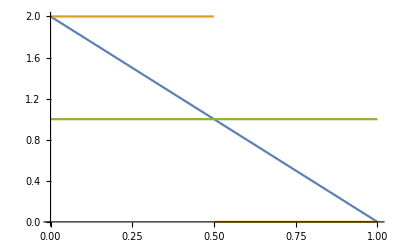

```mathematica
Plot[{PL[l],PM[l],PE[l]}/.L->1//Evaluate,{l,0,1}]
```

```mathematica
∫_0^L PL[l]ⅆl
```

1

With this we can easily derive the radius of gyration, again we have to take care of double counting of pairs hence the prefactor:

#### Form Factor

Using the Debye formula, we can calculate the scattering contribution between any two scatterers separated by a contour length L along a chain. Contrary to Rg, we count each pair twice when deriving the average scattering, hence there is no prefactor.

The scattering contribution for two scatterers a contour length l apart along the chain:

```mathematica
Ψ[l_]=∫_0^∞ P[r,l] Sin[q r]/(q r)ⅆr
```

ⅇ^(-1/6 b l q^2)

The form factor is the scattering due to pairs of contour distance l and averaged over all pairs along the chain up to length L:

```mathematica
f=∫_0^L Ψ[l]PL[l] ⅆl
```

-(72-72 ⅇ^(-1/6 b L q^2)-12 b L q^2)/(b^2 L^2 q^4)

We can simplify a lot by recognizing that the expression only depends on the dimensionless variable x defined as: x==q^2(b L)/6 = q^2 Rg^2

```mathematica
F=f/.q-> √((6 x)/(L b))//FullSimplify
```

(2 (-1+ⅇ^-x+x))/x^2

Reference Debye form factor: The form factor of a polymer was first derived in P . Debye, J . Phys. Colloid Chem. 51, 18 (1947) .

#### Form factor amplitude relative to ends

The form factor amplitude relative to a reference point at  l1 = 0 is the scattering averaged over a uniform distribution of all scatterers at l2 in [0:Ltot], hence L=l2-l1=l2:

```mathematica
Aend1=1/L∫_0^L Ψ[l2-0] ⅆl2/.q-> √((6 x)/(L b))//Simplify
```

(1-ⅇ^-x)/x

References for this expression : B . Hammouda, J . Polym . Sci ., Part B : Polym. Phys . 30, 1387 (1992) .

We can also calculate the form factor amplitude relative to the other end of the chain, hence l2=Ltot, and we average l1 over an uniform distribution [0:Ltot] hence L=l2-l1=Ltot-l1. Obviously we get the same result, since all chain observables are  symmetric wrt. swapping the identity of the ends.

```mathematica
Aend2=1/L∫_0^L Ψ[L-l1] ⅆl1/.q-> √((6 x)/(L b))//Simplify
```

(1-ⅇ^-x)/x

#### Phase factor between the ends

The phase factor is calculated for l1=0 and L2=Ltot, hence L=Ltot without any averaging:

```mathematica
Psiend1end2=Ψ[L]/.q-> √((6 x)/(L b))//Simplify
```

ⅇ^-x

Reference : This was already used by Debye to derive the form factor, but in the context of having the complete scattering expressions for a polymer "A formalism for scattering of complex composite structures. I. Applications to branched structures of asymmetric sub-units" C . Svaneborg and J . S . Pedersen J . Chem . Phys . 136, 104105 (2012) DOI : http : // dx . doi . org/10.1063/1.3682778

#### Form Factor amplitude and phase factors relative to a middle reference point .

Assuming we place a reference point at L/2, what are the form factor amplitude and phase factors?

```mathematica
Amiddle=1/L∫_0^L Ψ[Abs[L/2-l1]] ⅆl1/.q-> √((6 x)/(L b))//Simplify
```

(2-2 ⅇ^(-x/2))/x

```mathematica
Psimiddle2end=Ψ[L/2]/.q-> √((6 x)/(L b))//Simplify
```

ⅇ^(-x/2)

#### Contour distributed reference points :

To calculate the form factor amplitude relative to a uniformly distributed reference point l1 in [0 : L], and a uniformly distributed scatterer l2 in [0 : L] we again perform a double average of f[l] using the distribution of random pair distances PL[l] derived above

```mathematica
Acontour=∫_0^L Ψ[l] PL[l]ⅆl/.q-> √((6 x)/(L b))//FullSimplify
```

(2 (-1+ⅇ^-x+x))/x^2

We recognize that the form factor amplitude averaged over random reference points produce the Debye form factor, since it is exactly the same averages that we perform.

To calculate the average phase factor between the end (l1 = 0) and a uniformly distributed reference point at l2 in [0 :L]:

```mathematica
Psiend1contour=1/L∫_0^L Ψ[l2-0]ⅆl2/.q-> √((6 x)/(L b))//Simplify
```

(1-ⅇ^-x)/x

To calculate the average phase factor between the other end (l2 = L) and a uniformly distributed reference point at l1 in [0 : L]:

```mathematica
Psiend2contour=1/L∫_0^L Ψ[L-l1]ⅆl1/.q-> √((6 x)/(L b))//Simplify
```

(1-ⅇ^-x)/x

Again we recognize that both averages gives exactly the same result, since polymer observables are symmetric wrt . the ends . We also note that the phase factor between an end and an random internal site is  identical to the form factor amplitude derived above, since in fact its the same average we perform.

Finally we derive the phase factor between two randomly picked points along the contour length of the chain . Hence l1 and l2 are both uniform distributed in [0 : L]:

```mathematica
Psicontour2contour=1/L^2∫_0^L ∫_0^L Ψ[Abs[l2-l1]]ⅆl2ⅆl1/.q-> √((6 x)/(L b))//FullSimplify
```

(2 (-1+ⅇ^-x+x))/x^2

Again as expected this is again identical to the form factor, since its the same averages involved in its derivation .

Finally, we need the phase factor between the middle point, and any site along the polymer:

```mathematica
Psimiddle2contour=1/L∫_0^L Ψ[Abs[L/2-l1]]ⅆl1/.q-> √((6 x)/(L b))//Simplify
```

(2-2 ⅇ^(-x/2))/x

#### Plots

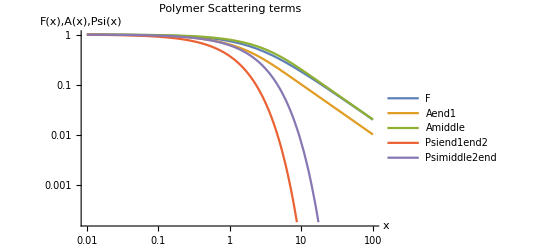

```mathematica
LogLogPlot[{F,Aend1,Amiddle,Abs[Psiend1end2],Abs[Psimiddle2end]},{x,0.01,100},PlotLabel-> "Polymer Scattering terms",AxesLabel-> {"x","F(x),A(x),Psi(x)"},PlotLegends->{"F","Aend1","Amiddle","Psiend1end2","Psimiddle2end"}]
```

#### Guinier - expansion form factor

```mathematica
Clear[Rg2]
```

Above we derived the mean - square distances explicitly. Here we show how to obtain these from a Guinier expansion of the various scattering terms.

The Guinier expansion of F is
1 - q^2 Rg^2 / 3 + O(q^4)

```mathematica
Series[F/.x-> q^2 Rg2,{q,0,3}]
```

1-(Rg2 q^2)/3+O[q]^4

Hence to isolate the radius of gyration in the series:

```mathematica
(3(1-Normal[Series[F/.x-> q^2 Rg2,{q,0,3}]]))/q^2
```

Rg2

#### Guinier - expansions amplitudes and phase factors

The Guinier expansion of A and Psi are :   1 - q^2 σ<R^2> / 6 + O(q^4).

The strange difference between the Guinier expansions  of Form Factor and amplitude and phase, stems from the 1/2 in the definition of the radius of gyration, since we define the Rg such that pair distances are unique.

```mathematica
Amplitudes. Sigma=1 except for Acontour
```

Amplitudes

```mathematica
Solve[Normal[Series[Aend1/.x-> q^2 Rg2,{q,0,3}]]==1-(q^2 σR2)/6,σR2]
```

{{σR2→3 Rg2}}

```mathematica
Solve[Normal[Series[Amiddle/.x-> q^2 Rg2,{q,0,3}]]==1-(q^2 σR2)/6,σR2]
```

{{σR2→(3 Rg2)/2}}

```mathematica
Solve[Normal[Series[Acontour/.x-> q^2 Rg2,{q,0,3}]]==1-(q^2 σR2)/6,σR2]
```

{{σR2→2 Rg2}}

```mathematica
Phases. sigma=1 except for Psicontour2contour
```

Phases

```mathematica
Solve[Normal[Series[Psiend1end2/.x-> q^2 Rg2,{q,0,3}]]==1-(q^2 σR2)/6,σR2]
```

{{σR2→6 Rg2}}

```mathematica
Solve[Normal[Series[Psimiddle2end/.x-> q^2 Rg2,{q,0,3}]]==1-(q^2 σR2)/6,σR2]
```

{{σR2→3 Rg2}}

```mathematica
Solve[Normal[Series[Psiend1contour/.x-> q^2 Rg2,{q,0,3}]]==1-(q^2 σR2)/6,σR2]
```

{{σR2→3 Rg2}}

```mathematica
Solve[Normal[Series[Psimiddle2contour/.x-> q^2 Rg2,{q,0,3}]]==1-(q^2 σR2)/6,σR2]
```

{{σR2→(3 Rg2)/2}}

```mathematica
Solve[Normal[Series[Psicontour2contour/.x-> q^2 Rg2,{q,0,3}]]==1-(q^2 σR2)/6,σR2]
```

{{σR2→2 Rg2}}

#### Save example data to file for Validation :

```mathematica
SaveFunction[func_,filename_,NN_,qmin_,qmax_]:=Module[{},Export[filename,{#,N[func/.q-> #]}&/@Table[10^(Log[10,qmax/qmin]*i/NN+Log[10,qmin]),{i,0,NN}]]]
```

```mathematica
SaveFunction[F/.x-> q^2 Rg2/.Rg2->1 ,"/home/zqex/source/SEB/source/Validation/RWpolymer_mathematica/F.dat",200,0.01,20]
```

/home/zqex/source/SEB/source/Validation/RWpolymer_mathematica/F.dat

```mathematica
SaveFunction[Aend1/.x-> q^2 Rg2/.Rg2->1 ,"/home/zqex/source/SEB/source/Validation/RWpolymer_mathematica/Aend.dat",200,0.01,20]
SaveFunction[Amiddle/.x-> q^2 Rg2/.Rg2->1 ,"/home/zqex/source/SEB/source/Validation/RWpolymer_mathematica/Amiddle.dat",200,0.01,20]
```

/home/zqex/source/SEB/source/Validation/RWpolymer_mathematica/Aend.dat

/home/zqex/source/SEB/source/Validation/RWpolymer_mathematica/Amiddle.dat

```mathematica
SaveFunction[Psiend1end2/.x-> q^2 Rg2/.Rg2->1 ,"/home/zqex/source/SEB/source/Validation/RWpolymer_mathematica/Psi_end2end.dat",200,0.01,20]
SaveFunction[Psimiddle2end/.x-> q^2 Rg2/.Rg2->1 ,"/home/zqex/source/SEB/source/Validation/RWpolymer_mathematica/Psi_middle2end.dat",200,0.01,20]
SaveFunction[Psimiddle2contour/.x-> q^2 Rg2/.Rg2->1 ,"/home/zqex/source/SEB/source/Validation/RWpolymer_mathematica/Psi_middle2contour.dat",200,0.01,20]
```

/home/zqex/source/SEB/source/Validation/RWpolymer_mathematica/Psi_end2end.dat

/home/zqex/source/SEB/source/Validation/RWpolymer_mathematica/Psi_middle2end.dat

/home/zqex/source/SEB/source/Validation/RWpolymer_mathematica/Psi_middle2contour.dat